```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/results.json"];
raw = Association[#]&/@raw;
```

```mathematica
maxDistance[pts_]:=(
Flatten[Table[
Norm[pt1-pt2],
{pt1, pts},
{pt2,pts}
]]//Max
)
```

## At PENT

```mathematica
data =GroupBy[raw,{#quadErrorSigma, #iteration}&];

Table[
data[key]=maxDistance[{#["PENT_xCenter"],#["PENT_yCenter"]}&/@data[key]];
Nothing,
{key,Keys[data]}
];
```

```mathematica
quadErrorSigmaValues = DeleteDuplicates[Keys[data][[All,1]]]
iterationValues = DeleteDuplicates[Keys[data][[All,2]]]
```

{1.×10^-6,2.×10^-6,5.×10^-6,0.00001,0.00002,0.00005,0.0001,0.0002,0.0005}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

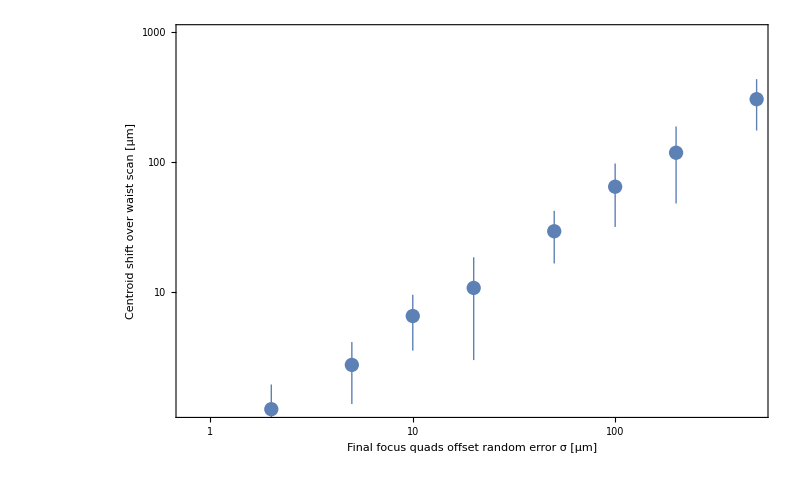

```mathematica
groupedData = Table[
{
quadErrorSigma,
Around[
Table[
data[{quadErrorSigma,iteration}],
{iteration,iterationValues}
]
]
},
{quadErrorSigma,quadErrorSigmaValues}
];



ListLogLogPlot[
10^6 groupedData,
ImageSize->800,
PlotRange->{0,1000},
LabelStyle->20,
Frame->True,
FrameLabel->{"Final focus quads offset \n random error σ [μm]", "Centroid shift over waist scan [μm]"}
]
```

## At waist

```mathematica
data =GroupBy[raw,{#quadErrorSigma, #iteration}&];

Table[
data[key]=maxDistance[{#["PENT_offset_xCenter"],#["PENT_offset_yCenter"]}&/@data[key]];
Nothing,
{key,Keys[data]}
];
```

```mathematica
quadErrorSigmaValues = DeleteDuplicates[Keys[data][[All,1]]]
iterationValues = DeleteDuplicates[Keys[data][[All,2]]]
```

{1.×10^-6,2.×10^-6,5.×10^-6,0.00001,0.00002,0.00005,0.0001,0.0002,0.0005}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

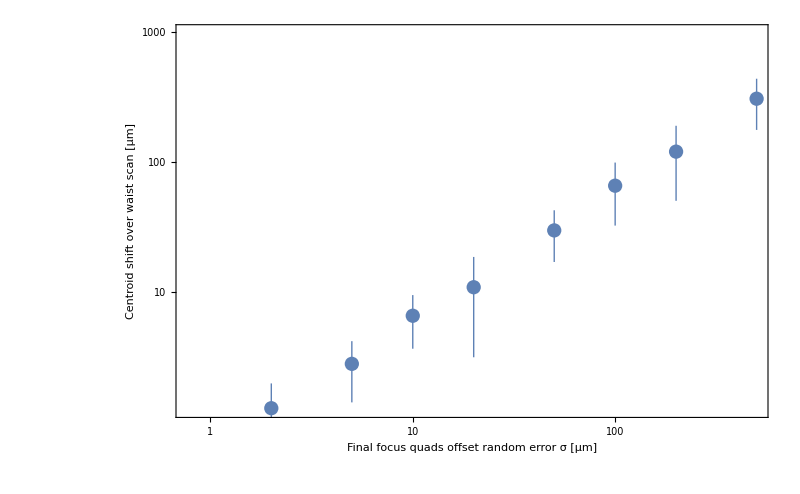

```mathematica
groupedData = Table[
{
quadErrorSigma,
Around[
Table[
data[{quadErrorSigma,iteration}],
{iteration,iterationValues}
]
]
},
{quadErrorSigma,quadErrorSigmaValues}
];



ListLogLogPlot[
10^6 groupedData,
ImageSize->800,
PlotRange->{0,1000},
LabelStyle->20,
Frame->True,
FrameLabel->{"Final focus quads offset \n random error σ [μm]", "Centroid shift over waist scan [μm]"}
]
```